```mathematica
funkcijaT[f_,t_,t0_,red_]:=Module[{taylorjevaVrsta},
taylorjevaVrsta=Normal[Series[f,{t,t0,red}]];

Plot[{f,taylorjevaVrsta},{t,0,4}, PlotLegends->Placed[{"Originalna funkcija","Aproksimacija"},Below],
AxesLabel->{"t","f(t)"},
PlotRange->{{0,4.5},{-.4,1}}

]
]

f[t_]= Sin[t] t^2 Exp[-t];
t0=2;
```

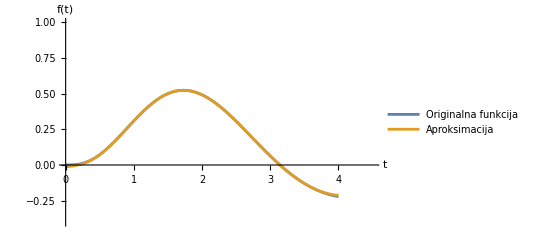

```mathematica
funkcijaT[f[t],t,t0, 10]
```

```mathematica
Manipulate[
funkcijaT[f[t],t,t0,red],{{red,6,"Red pribljižka"},1,10,1},FrameLabel->{"Pribljižek funkcije pri različnih redih"}
]
```

```mathematica
Ž
```